```mathematica
Get["para.m",Path-> NotebookDirectory[]]
```

para: A Mathematica package for inputting Standard Model parameters

by Yang Ma (March 2020)

If you use para in your research, please cite

• T. Han, Y. Ma, and K. Xie, Phys.Rev.D 103 (2021) 3, L031301, arXiv:2007.14300.

• T. Han, A. K. Leibovich, Y. Ma and X.-Z. Tan, JHEP 08 (2022) 073, arXiv:2202.08273.

```mathematica
(* Defined colors for plot*)
{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11}
```

{RGBColor[Rational[76, 85], Rational[26, 255], Rational[28, 255]],RGBColor[Rational[77, 255], Rational[35, 51], Rational[74, 255]],RGBColor[Rational[11, 51], Rational[42, 85], Rational[184, 255]],RGBColor[1, Rational[127, 255], 0],RGBColor[Rational[152, 255], Rational[26, 85], Rational[163, 255]],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[Rational[41, 255], Rational[143, 255], 1],RGBColor[Rational[128, 255], 0, Rational[128, 255]],RGBColor[Rational[166, 255], Rational[86, 255], Rational[8, 51]],RGBColor[1, Rational[1, 3], 1]}

```mathematica
(* SM parameters *)
SMinput
```

{g→0.653226026666386948500864273768313162452096718235,CW→0.8818940270527577617901159936092909196721774828588,SW→0.471447690681235346101654222751891195090168496619,CA→3,EL→0.30796190176474718587556594832554700712923265642294,MW→80.41815253888687478211709722524402038306652030692,αE→0.0075471698113207547169811320754716981132075471698113,GF→0.0000116639,Mt→172.,MB→4.7,MC→1.5,MA→0,MZ→91.188,MH→125.,MM→0.10566,ME→0.000511,GammaZ→2.4414,GammaW→2.0476,GammaT→1.50834,GammaH→0.00575309,Vcb→0.041}

```mathematica
(* QCD sector *)
QCDpara
```

{CF→4/3,CA→3}

```mathematica
(* LO QCD coupling *)
αs0[3]//N
(* NLO QCD coupling *)
αs1[3]//N
αs[3]//N
```

0.235326

0.256845

0.251448

Warning: it is dangerous to use the value of αs(Q) when Q < 1 GeV

Warning: it is dangerous to use the value of αs(Q) when Q < 1 GeV

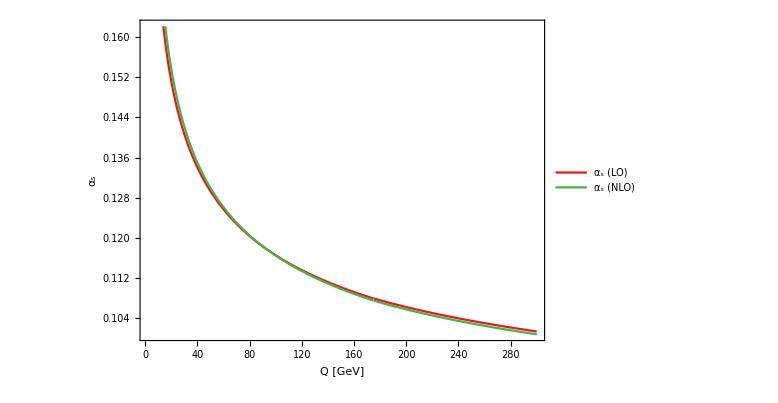

```mathematica
(* QCD coupling running *)
Plot[{αs0[Q],αs1[Q]},{Q,2,300},PlotStyle->{{c1},{c2},{c3},{c1,Dashed},{c2,Dashed},{c3,Dashed}},PlotLegends->Placed[LineLegend[{"α_s (LO)","α_s (NLO)"},LegendLayout->{"Column",1}],{0.68,0.38}],FrameLabel->{"Q [GeV]","α_s"},AspectRatio->0.7/1]
```

```mathematica
(* Gauge couplings running *)
```

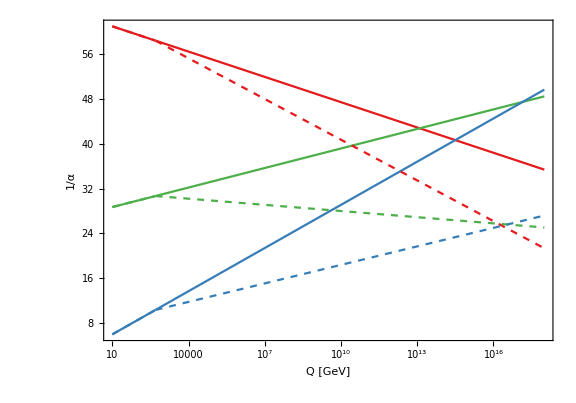

```mathematica
LogLinearPlot[{4π/gISM2[Log[e],1],4π/gISM2[Log[e],2],4π/gISM2[Log[e],3],4π/gIMSSM2[Log[e],1],4π/gIMSSM2[Log[e],2],4π/gIMSSM2[Log[e],3]},{e,10,10^18},PlotStyle->{{c1},{c2},{c3},{c1,Dashed},{c2,Dashed},{c3,Dashed}},FrameLabel->{"Q [GeV]","1/α"},AspectRatio->0.7/1]
```

```mathematica
(* Charm quark and bottom quark running mass at LO *)
MH=125;
LOmcMS[MH]
LOmbMS[MH]
```

0.69418877479479783957083525576023128512180116293932

2.9044912601499742886789682089578659658873271466792

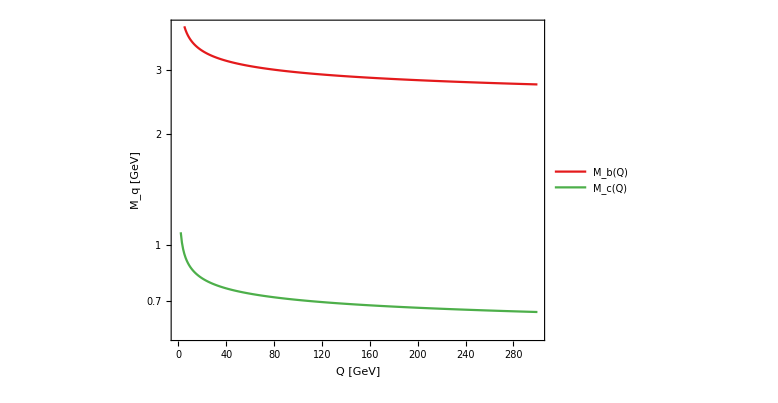

```mathematica
tabMc=Table[{Q,LOmcMS[Q]},{Q,2,300}];
tabMb=Table[{Q,LOmbMS[Q]},{Q,5,300}];
ListLogPlot[{tabMb,tabMc},PlotStyle->{c1,c2},PlotLegends->Placed[LineLegend[{"M_b(Q)","M_c(Q)"},LegendLayout->{"Column",1}],{0.68,0.38}],FrameLabel->{"Q [GeV]","M_q [GeV]"},AspectRatio->0.7/1]
```